{0.1880336115708795609315551561953,0.1315968811280182898995570113772,0.091771243880853153103578564147,0.0637703521715097778660461605902,0.044155234974430996222411711857,0.030464653693795094071111492047,0.02094398222163763453146847817,0.0143471959665378191220305061,0.0097928665729995460780757818,0.0066598720288227923112229002,0.0045121826182287371998385439,0.003044837975775376394333411,0.00204529837875454213928091,0.00136589740554235840861002,0.00090426942182679117512445,0.00058947103626613108176443,0.0003721345287891882852433,0.000217438762924299347726,0.000100000000004502545065,6.796697532×10^-15}

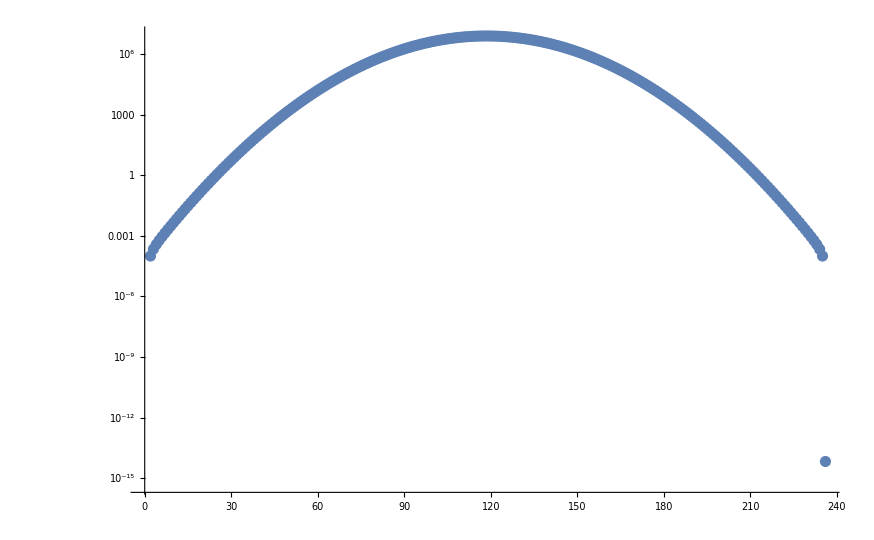

```mathematica
mass=2;
V[r_]=(r-15)^2;
xmin=10;
xmax=20;
nOfPoints=236;
stepSize=(xmax-xmin)/(nOfPoints-1);
energy=0.4998868009845387437379292574102`110;
Q[r_]=2mass*(energy-V[r]);
ψ=Table[0,{nOfPoints}];
ψ[[1]]=0;
ψ[[2]]=10^-4;
Do[ψ[[j+1]]=ψ[[j]](2-stepSize^2*Q[xmin +stepSize(j-1)])-ψ[[j-1]],{j,2,nOfPoints-1}];
(* integral=(Sum[ψ[[j]]^2,{j,2,nOfPoints-1}]+ψ[[nOfPoints]]^2/2)stepSize
ψ=ψ/√integral;*)
Take[ψ,-20]
ListLogPlot[ψ]
```

```mathematica
f=Interpolation[Table[{xmin +stepSize(j-1),ψ[[j]]},{j,1,nOfPoints}],InterpolationOrder->3,Method->"Spline"];
```

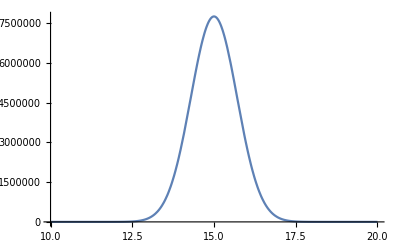

```mathematica
Plot[f[x],{x,10,20},PlotRange->All]
```